#### When does λ_TF = λ_e? Critical density when radiative processes “shut off”

```mathematica
Solve[λTF==1/me/.{Ef->(3 Pi^2 n)^(1/3)},n]
```

{{n→-me^3/(6 √(2 π) Z^(3/2) α^(3/2))},{n→me^3/(6 √(2 π) Z^(3/2) α^(3/2))}}

```mathematica
Convert[(me^3/(6 √(2 π) Z^(3/2) α^(3/2))/.{me->0.511,α->1/137,Z->6})(Mega ElectronVolt)^3*(200Mega ElectronVolt*Fermi)^-3,Centimeter^-3]
```

(1.21×10^32)/Centimeter^3

#### Typiacl Ion Plasma Frequency in relevant range of WD densities.

```mathematica
{Convert[((ni Z^2 e^2)/mi)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{ni->10^29 Centimeter^-3,mi->12Giga ElectronVolt,e->0.3,Z->6},Kilo ElectronVolt],Convert[((ni Z^2 e^2)/mi)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{ni->10^31 Centimeter^-3,mi->12Giga ElectronVolt,e->0.3,Z->6},Kilo ElectronVolt]}
```

{0.464758 ElectronVolt Kilo,4.64758 ElectronVolt Kilo}

#### Classic EM cascades:

```mathematica
BH=(k^2/e^2+2 (1+(1-k/e)^2))/(3 k n X0);
```

```mathematica
Integrate[BH*n*k,{k,0,e}]
```

e/X0

```mathematica
PP=(1+2 ((1-e/k)^2+e^2/k^2))/(3 k n X0);
```

```mathematica
Integrate[PP,{e,0,k}]
```

7/(9 n X0)

#### LPM suppression

```mathematica
Solve[k<e^2/elpm,k]
```

Solve::fdimc: When parameter values satisfy the condition (e>0&&elpm>0)||(elpm<-e&&e>0)||(-e<elpm<0&&e>0)||(e<0&&elpm>-e)||(e<0&&elpm<0)||(0<elpm<-e&&e<0), the solution set contains a full-dimensional component; use Reduce for complete solution information.

{}

```mathematica
bremlosszero=Integrate[(√((Elpm k)/(e (e-k))) (k^2/e^2+2 (1+(1-k/e)^2)))/(3 k n X0)*k*n,{k,0,e}];
```

```mathematica
bremlosszero//N
```

(1.50535 e √(Elpm/e))/X0

```mathematica
bremeloss=Integrate[(√((Elpm k)/(e (e-k))) (k^2/e^2+2 (1+(1-k/e)^2)))/(3 k n X0)*k*n,k];
```

```mathematica
Limit[bremeloss,k->e]
```

-(23 √-e √-Elpm π)/(48 X0)

```mathematica
eloss=Limit[bremeloss,k->e]-Limit[bremeloss,k->kmin];
```

```mathematica
eloss/.{Elpm->0.1,X0->500,kmin->10^-5 e}
```

(0.-0.000952065 ⅈ) √-e-1/e^(5/2)0.0000263524 √(1/e) (-(2874963750174999 e^(7/2))/(12500000000000000 √10)+69/100 √(11111/10) e^(5/2) √(e^2) ArcTan[e/(3 √11111 √(e^2))])

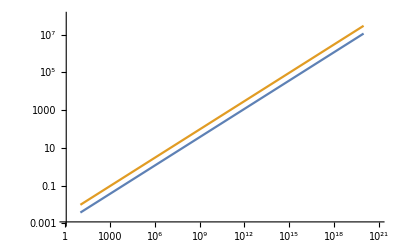

```mathematica
LogLogPlot[{(eloss/.{Elpm->1,X0->500,kmin->e/1.1}),(bremlosszero/.{Elpm->1,X0->500})},{e,10,10^20}]
```

#### When does λTF = Compton

```mathematica
Solve[λTF==1/me/.{Ef->(3 Pi^2*n)^(1/3)},n]
```

{{n→-m^3/(6 √(2 π) Z^(3/2) α^(3/2))},{n→m^3/(6 √(2 π) Z^(3/2) α^(3/2))}}

```mathematica
m^3/(6 √(2 π) Z^(3/2) α^(3/2))/.{m->0.511,α->1/137,Z->6}//N
```

```mathematica
Convert[(m^3/(6 √(2 π) Z^(3/2) α^(3/2))/.{m->0.511,α->1/137,Z->6})(Mega ElectronVolt)^3*(200Mega ElectronVolt*Fermi)^-3,Centimeter^-3]
```

(1.21×10^32)/Centimeter^3

```mathematica
1/X0=4n Z^2 α^3/me^2
```

```mathematica
(me^2*α*X0)/(4Pi)/.{X0->(4n Z^2 α^3/me^2)^-1}//FullSimplify
```

```mathematica
<<Units`
```

```mathematica
Convert[me^4/(16 n π Z^2 α^2)*(200Mega ElectronVolt*Fermi)^-3/.{me->100Mega ElectronVolt,n->10^31 Centimeter^-3,Z->6,α->1/137},Mega ElectronVolt]//N
```

1.29652×10^10 ElectronVolt Mega

#### Plasma Frequency

```mathematica
Convert[((ni*Z^2 e^2)/mi)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{ni->10^31 Centimeter^-3,mi->12Giga ElectronVolt,e->0.3,Z->6},Kilo ElectronVolt]
```

4.64758 ElectronVolt Kilo